```mathematica
This is a text cell. My name is Kristina Ilyovska.
```

Syntax::sntxi: Incomplete expression; more input is needed .

## Section 1: Basic Computations

```mathematica
Sin[2Pi/3]
Sqrt[80089]
ArcTan[2.4]
```

(√3)/2

283

1.17601

## Section 2: Using the Palettes

```mathematica
Cos[(81π)/4]
∫_0^4 (x+1)^12 ⅆx
D[((x^2+ y^2)/x), x]
```

1/(√2)

1220703124/13

2-(x^2+y^2)/x^2

## Section 3: Calculus

```mathematica
f[x_,y_] := x^2-Sin[2y]
```

```mathematica
fxDerivative := D[f[x,y],x]
fxDerivative
fyyDerivative:= D[f[x,y],y,y]
fyyDerivative
```

2 x

4 Sin[2 y]

```mathematica
fxDerivative/.{x->0, y->1}
fyDerivative := D[f[x,y],y]
fyDerivative/.{x-> 0, y->1}
```

0

-2 Cos[2]

```mathematica
g[x_]:= f[x,1]
gxDerivative := D[g[x],x]/.{x->0}
gxDerivative
```

0

```mathematica
h[y_] := f[0,y]
hyDerivative := D[h[y],y]/.{y->1}
hyDerivative
```

-2 Cos[2]

## Section 4: Plotting

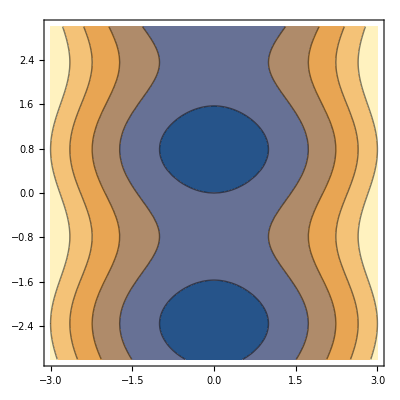

```mathematica
ContourPlot[f[x,y],{x, -3,3}, {y,-3,3}]
```

```mathematica
functionPlot := Plot3D[f[x,y],{x,-3,3},{y,-3,3}, Mesh->None, PlotStyle->Blue]
functionPlot
```

-Graphics3D-

```mathematica
a=1;
r[t_,a_]:= {t, a,f[t,1]}
```

```mathematica
b=0;
s[t_,b_]:= {b, t,f[0,t]}
```

```mathematica
curve1= ParametricPlot3D[r[x], {x,-3, 3}, {y,-3, 3}]
curve2 = ParametricPlot3D[s[y], {x,-3, 3}, {y,-3, 3}]
```

-Graphics3D-

-Graphics3D-

```mathematica
completePlot:= Show[functionPlot,curve1, curve2]
completePlot
```

-Graphics3D-

```mathematica
f[x_,y_]= x^2-Sin[2y]
Manipulate[
Show[
 Plot3D[x^2-Sin[2y], {x,-3,3},{y,-3,3}, Mesh -> None],
ParametricPlot3D[ {t, a,f[t,a]}, {t,-3, 3}, PlotStyle->{Black,Thick}],
ParametricPlot3D[{b, t,f[b,t]}, {t,-3, 3}, PlotStyle -> {Black, Thick}]
]
, {a,-3,3}, {b,-3,3}
]
```

x^2-Sin[2 y]

The assignment was very good and doable intro to Mathematica that provided me with some insight into the syntax, into how to compile the code, and the scope of the defined variables. Learning to execute each cell before proceeding was the major problem for me. I generally worked on my own and then had some help from Bob (in our class) towards the end of the project in catching some wrong parameters in the vector functions. The whole project didn’t take more than a couple of hours with the debugging.